```mathematica
a=Get["/home/drchaj1/java/ne/fc.txt"];
```

```mathematica
MatrixForm[a];
```

```mathematica
Length[a]
```

147

```mathematica
plotSandwich[m_]:=
ArrayPlot[m,ColorRules->{Max[m]->Red},Mesh->True]
```

```mathematica
Grid[Partition[Sequence@@{ArrayPlot[#⟦1⟧, Mesh->True], plotSandwich[#⟦2⟧]}&/@a,2]]
```

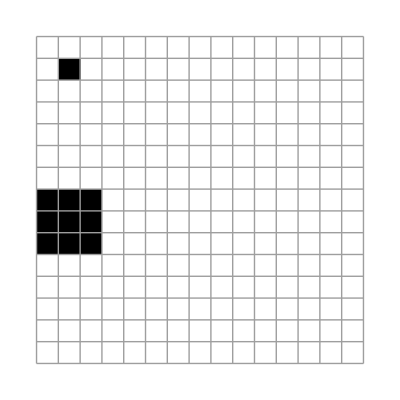
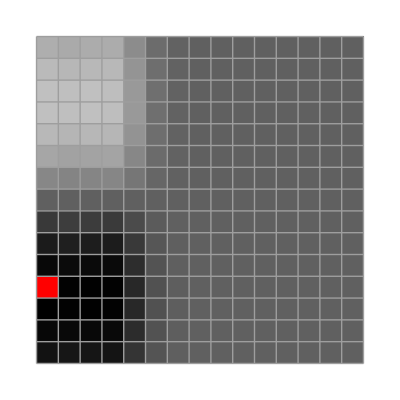
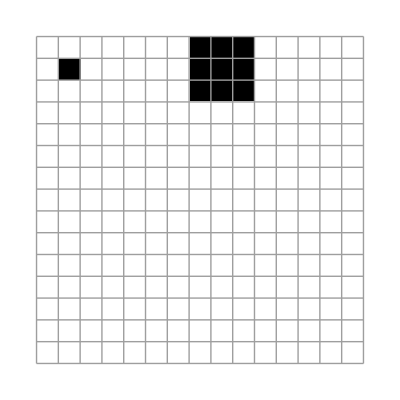
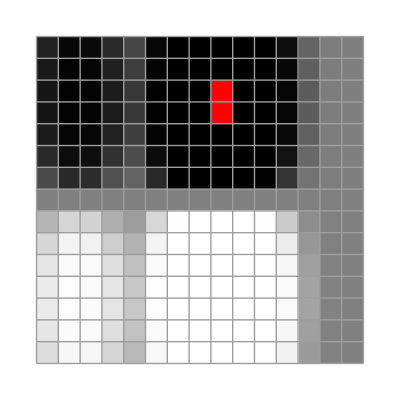
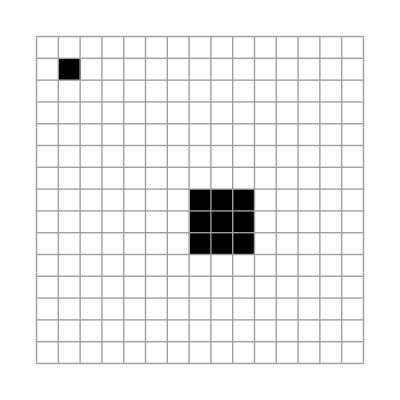
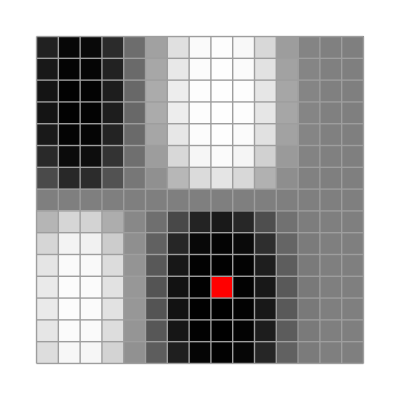
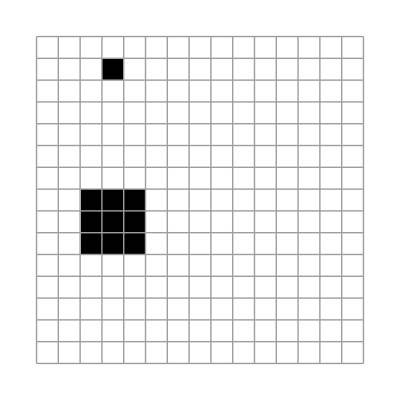
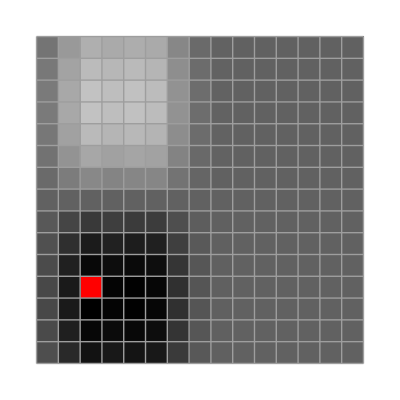
```mathematica
{{-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}, {-Graphics-, -Graphics-}}git clone http://drchal.felk.cvut.cz/git/ne.git
```